# Cinemática de Medios Continuos

## Conjuntos discretos de partículas vs. medios continuos

1. Es habitual que la cinemática de una partícula  sea descrita por medio de un vector de posición que depende del tiempo:
r = r(t)

donde r(t) = x_1(t) e_1+ x_2(t)e_2 + x_3(t)e_3

2.. Si hay N partículas, entonces cada una tiene su vector:

r_n= r_n(t)  ; n = 1,2,3,....,N

En un medio continuo finito, hay infinitas partículas, por lo tanto no es posible enumerarlas por medio del conjunto de los números naturales 𝒩, y se pasa a un conjunto que conocemos (!?) más que ningún otro: una partícula específica en el continuo queda determinada por un valor real de sus coordenadas (ℛ^3) en un tiempo de referencia t_0.

En un continuo tenemos que la posición de una partícula X está determinada por un vector x, el cual depende tanto del tiempo (se desplaza) como de la partícula del continuo (se deforma, se mueven sus partes relativamente).

x(X,t) con X = x(X,t_0)

En forma de componentes, la ec. anterior se lee:

## Descripciones de la cinemática de medios continuos:

Suponiendo que un medio continuo está en movimiento, y que ciertas propiedades cambian con el tiempo, como por ejemplo, la temperatura Θ, la velocidad v o el esfuerzo T (capítulo siguiente), entonces tenemos dos formas de describir estos cambios:

1. Descripción Material o Lagrangiana: Se describe el cambio desde el punto de vista de las partículas, es decir, se obtienen funciones como:

v̂(X_1,X_2,X_3, t)
Θ̂(X_1,X_2,X_3, t)
T̂(X_1,X_2,X_3, t)

2. Descripción espacial o Euleriana: se describe el cambio en un punto del espacio fijo (como el sistema de referencia del laboratorio), es decir, se obtienen funciones como:

```mathematica
ṽ(Subscript[x, 1],Subscript[x, 2],Subscript[x, 3], t)
Θ̃(Subscript[x, 1],Subscript[x, 2],Subscript[x, 3], t)
T̃(Subscript[x, 1],Subscript[x, 2],Subscript[x, 3], t)
```

Estas dos formas son equivalentes, pero es importante saber ir de una a la otra (contar el cuentito de la partícula que sale de X...)

### Derivada Material

La tasa de cambio de una magnitud respecto del tiempo de una partícula,  se denomina derivada material  y se denota por D /Dt. 

La forma de calcularla es:

1. Con la descripción material:

2. Con la descripción espacial:

-Graphics-

-Graphics-

Esto termina en que ∂x_i/∂t = v_i, entonces:

-Graphics-

Con notación de índices tenemos:

-Graphics-

En notación directa tenemos:

-Graphics-

### Ejemplo

Mirar: aceleración  de una partícula

--------------------------------------------------------------
-Graphics-

-Graphics-

tenemos entonces el campo de aceleración:

-Graphics-

-Graphics-

c) El gráfico de las aceleraciones nos da todo para el centro.

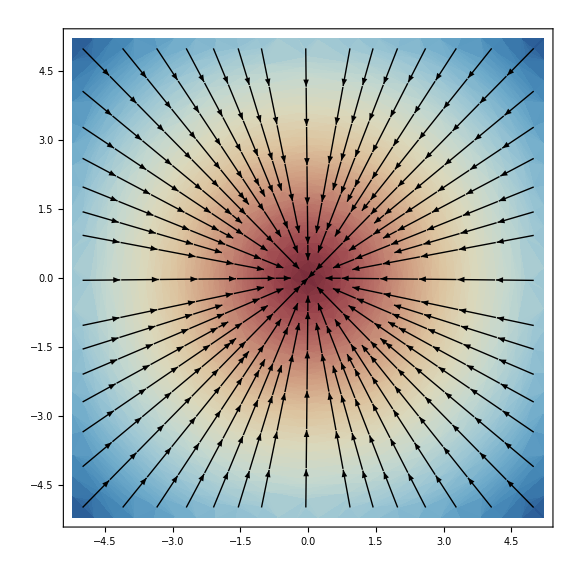

```mathematica
StreamDensityPlot[{{-4 x,-4 y},div[x,y]},{x,-5,5},{y,-5,5},ColorFunction-> "RedBlueTones",StreamStyle->Black,StreamPoints->Medium,ImageSize->Large]
```

c) el gráfico de las velocidades

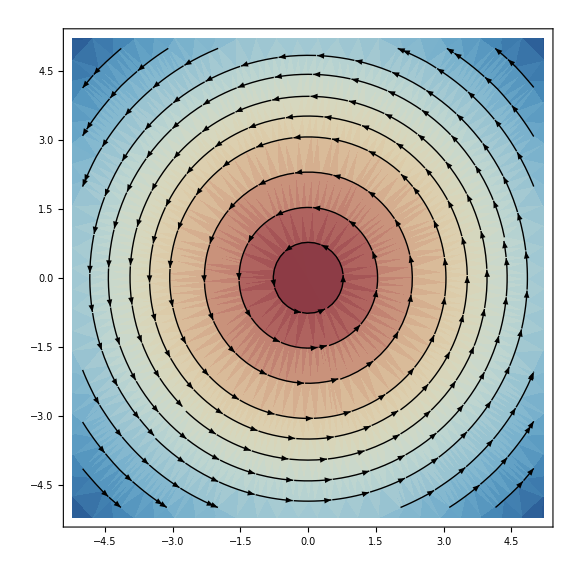

```mathematica
StreamDensityPlot[{{-2 y,2 x},div[x,y]},{x,-5,5},{y,-5,5},ColorFunction-> "RedBlueTones",StreamStyle->Black,StreamPoints->Medium,ImageSize->Large]
```

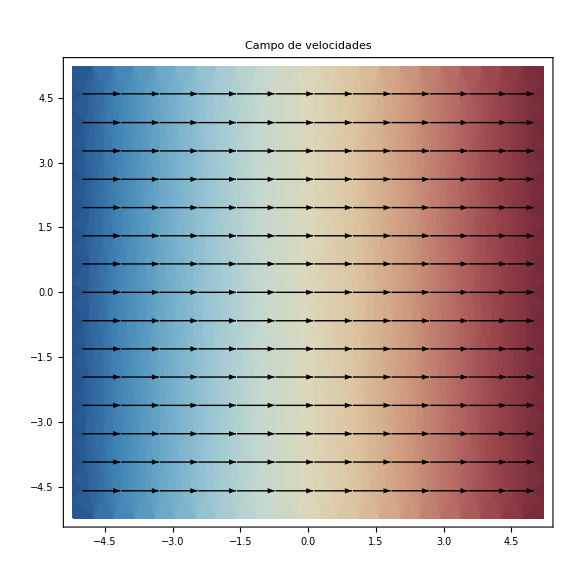

```mathematica
StreamDensityPlot[{{1,0},-x},{x,-5,5},{y,-5,5},ColorFunction-> "RedBlueTones",StreamStyle->Black,StreamPoints->Medium,ImageSize->Large,
PlotLabel-> "Campo de velocidades",LabelStyle->Directive[Bold,Orange]]
```